```mathematica
rawData=Import["/Users/skmcneill/Dropbox/NCETR R&D/Propane Oxygen/Pencil Probes/20140701_PropaneTank_Shot-1_PencilProbeData.csv", WordSeparators->{","},HeaderLines->1 ];
```

```mathematica
impulseData5x = Select[rawData,  #[[1]]≥0.0112785∧ #[[1]]≤ 0.0122395&][[All,{1,3}]];
```

```mathematica
impulseData5y = Select[rawData,  #[[1]]≥0.011132∧ #[[1]]≤ 0.0121480&][[All,{1,5}]];
```

```mathematica
impulseData10x = Select[rawData,  #[[1]]≥0.0146295∧ #[[1]]≤ 0.016109&][[All,{1,4}]];
```

```mathematica
impulseData10y = Select[rawData,  #[[1]]≥0.0145680∧ #[[1]]≤ 0.016146&][[All,{1,6}]];
```

```mathematica
f5x=Interpolation[impulseData5x]
```

InterpolatingFunction[{{0.0112785, 0.0122395}}, <>]

```mathematica
Derivative[-1][f5x]
```

InterpolatingFunction[{{0.0112785, 0.0122395}}, <>][#1]&

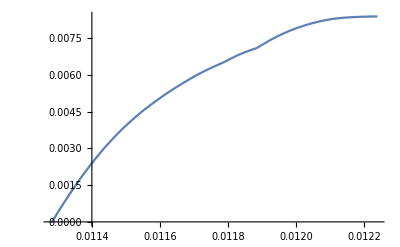

```mathematica
Plot[%279[x],{x,0.0112785,0.0122395}]
```

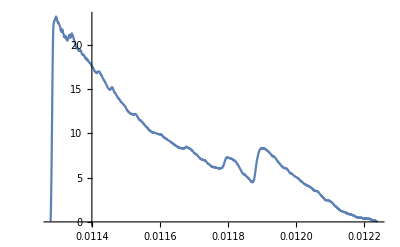

```mathematica
Plot[f5x[x],{x,0.0112785,0.0122395}]
```

```mathematica
f5y=Interpolation[impulseData5y]
```

InterpolatingFunction[{{0.011132, 0.012148}}, <>]

```mathematica
Derivative[-1][f5y]
```

InterpolatingFunction[{{0.011132, 0.012148}}, <>][#1]&

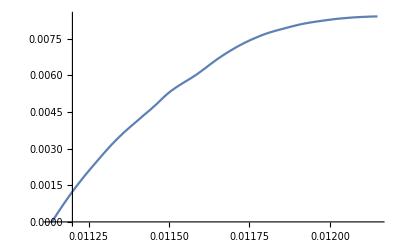

```mathematica
Plot[%282[x],{x,0.011132,0.012148}]
```

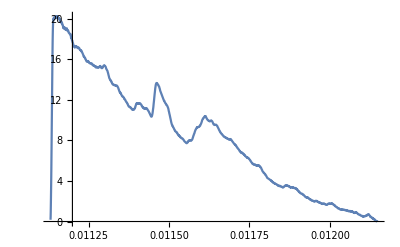

```mathematica
Plot[f5y[x],{x,0.011132,0.012148}]
```

```mathematica
f10x=Interpolation[impulseData10x]
```

InterpolatingFunction[{{0.0146295, 0.016109}}, <>]

```mathematica
Derivative[-1][f10x]
```

InterpolatingFunction[{{0.0146295, 0.016109}}, <>][#1]&

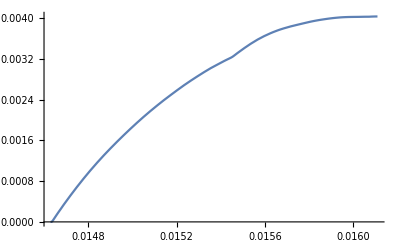

```mathematica
Plot[%285[x],{x,0.0146295,0.016109}]
```

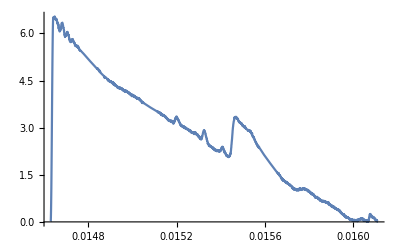

```mathematica
Plot[f10x[x],{x,0.0146295,0.016109}]
```

```mathematica
f10y=Interpolation[impulseData10y]
```

InterpolatingFunction[{{0.014568, 0.016146}}, <>]

```mathematica
Derivative[-1][f10y]
```

InterpolatingFunction[{{0.014568, 0.016146}}, <>][#1]&

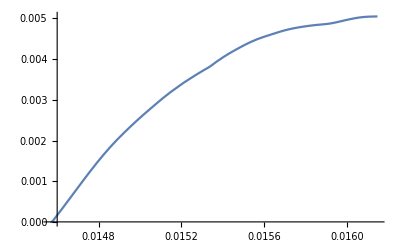

```mathematica
Plot[%288[x],{x,0.014568,0.016146}]
```

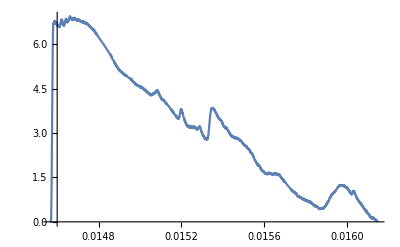

```mathematica
Plot[f10y[x],{x,0.014568,0.016146}]
```

```mathematica
NIntegrate[f5x[x],{x,0.0112785,0.0122395},AccuracyGoal->6]
```

0.00837759

```mathematica
NIntegrate[f5y[x],{x,0.011132,0.0121480},AccuracyGoal->6]
```

0.00840432

```mathematica
NIntegrate[f10x[x],{x,0.0146295,0.016109},AccuracyGoal->5]
```

0.00403478

```mathematica
NIntegrate[f10y[x],{x,0.0145680,0.016146},AccuracyGoal->5]
```

0.00504714